```mathematica
Clear["Global`*"]
```

# Check the three high points in the hf vs freq plot.

## Identify the planet and its properties. From the xmgrace hf vs freq.

```mathematica
approxFreq = {1.29 10^-4,2.54 10^-4, 3.88 10^-4};
approxhf = {6.38 10^-20, 1.74 10^-18, 2.96 10^-19}; (* approx freq for three points touching red LISA strain sensitivity curve on far right, taken from plot below *)
```

-Graphics-

The frequency ratios 1:2:3 indicate the same planet with an fr=1.29e-4 Hz.

```mathematica
perSecs = 1/approxFreq[[1]]
perDays = perSecs/3600.0/24.0
```

7751.94

0.0897215

As of 20160510.1100 the database, which is different now than the previous set that I used for my analysis indicates that the above is for Host Name PSR J1719-1438, currently rowid 1807.

```mathematica
plhostname = "PSR J1719-1438"; (* Underscores are NOT allowed! *)
plorbper = 0.090706; (* days, orbital period *)
plorbsmax = 0.0044; (* AU, orbit semi-major axis *)
plorbeccen = 0.06; (* orbital eccentricity *)
plbmassj = 1.2; (* Jupiter masses, planet mass *)
stdist = 1200; (* pc, stellar distance *)
stmass=1.4; (* Sun masses, stellar mass *);
```

Work in SI units.

```mathematica
massSun = 1.99 10^30; (*kg *)
massJ = 1.90 10^27; (* kg *)
massE = 5.97 10^24; (* kg *)
massJe = 317.9; (* earth masses *)
massJs = massJ/massSun; (* relative to the sun's mass *)
pc = 30.86 10^15; (* meters, parsec *)
au = 149.6 10^9; (* meters, astron unit *)
cee = 299792458.0; (* meters/s, speed of light *)
secsYear = 365.24*24.0*3600.0; (* s, number of seconds in a year *)
secsDay = 24.0*3600.0; (* s, number of seconds in a day *)
rscon = 2955.43; (* meters per solar mass, Schwarzschild radius *)
rscon = 2*6.67388 10^-11*massSun/cee^2 (* solar mass Scharzschild radius *)
lunits =6.67388 10^-11*massSun/cee^2 (* meters per solar mass, units of G=c=1 *)
bigG = 6.67384 10^-11; (* Gravitational constant, m^3/kg/s^2 *)
```

2955.43

1477.71

```mathematica
{cee, secsYear, rscon, lunits}
```

{2.99792×10^8,3.15567×10^7,2955.43,1477.71}

Use the full eccentricity formulae because we are checking the hv vs freq plot!

Max n from my formula, for the Peters & Mathews curve to come back down to 1/20 of the peak.  Used Nmax=3 if it was smaller.

```mathematica
nmaxFcn = E^# (0.589993-1.41201 # + 0.892102 #^2)&
```

ⅇ^#1 (0.589993-1.41201 #1+0.892102 #1^2)&

```mathematica
nmax = nmaxFcn[plorbeccen]
```

0.539927

```mathematica
nmax=3
```

3

Work in SI.

```mathematica
m1=stmass*massSun
m2 =plbmassj*massJ 
totMass = m1+m2
redMass = m1*m2/totMass
chirpMass = redMass^(3/5)totMass^(2/5)
dist = stdist*pc  (* m *)
period = plorbper*secsDay (* s *)
freq = 1/period (* Hz *)
```

2.786×10^30

2.28×10^27

2.78828×10^30

2.27814×10^27

3.91455×10^28

3.7032×10^19

7837.

0.0001276

Egads the A, B, and g(n,e) functions.  Put them in again!  Amaro-Seoane et al.’s form Eqns(4-6).

```mathematica
jj=BesselJ[#1, #2]&  (* Bessel function of integer order, this is a function definition *)
```

BesselJ[#1,#2]&

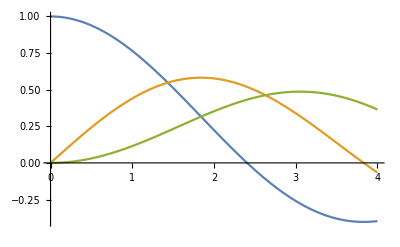

```mathematica
Plot[{jj[0,u], jj[1,u], jj[2,u]}, {u, 0, 4}]
```

```mathematica
bigA[n_, e_]:=jj[n-2,n e]-2 jj[n, n e]+jj[n+2,n e]
bigB[n_, e_]:=jj[n-2, n e]-2 e jj[n-1, n e]+2/n jj[n, n e]+2 e jj[n+1, n e]-jj[n+2, n e]
gg[n_, e_]:=n^4/32(bigB[n,e]^2+(1-e^2)bigA[n,e]^2+4/(3 n^2)jj[n,n e]^2)
```

Check versus the Peters&Mathews Fig. 3, also Maggiore page XX.

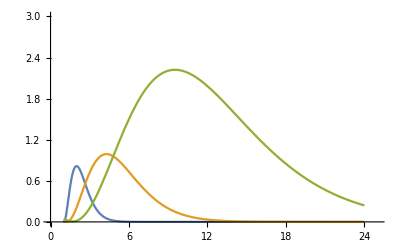

```mathematica
Plot[{gg[u,0.2], gg[u,0.5], gg[u, 0.7]},{u, 1, 24},
PlotRange->{{0,25},{0,3}}]
```

For this planet, AS eqn (9) gives h_n.

```mathematica
hh[n_]:=2 √(32/5) chirpMass^(5/3)/(n dist)(2π freq)^(2/3) √gg[n,plorbeccen]
```

```mathematica
Table[
{n, hh[n], bigG^(5/3)/cee^4 hh[n]},{n, 1, 3}
]//TableForm
```

1 | 1.2386×10^25 | 1.68374×10^-26
2 | 2.63685×10^26 | 3.5845×10^-25
3 | 3.56137×10^25 | 4.84129×10^-26

AS eqn(10), the observed strain, not strain sensitivity!
h_(obs,n)=h_n √(T f_(r,n))  where T=max(T_orb,T_obs) .
I plotted the 10 year observation for the strain sensitvity.
T_obs for LISA is either 3, 5, 10 years.

Factor is

```mathematica
afac[n_]:=√(n freq 10.0 secsYear)
```

```mathematica
afac[{1,2,3}]
```

{200.665,283.783,347.562}

```mathematica
bfac =√(10.0 secsYear)
```

17764.2

```mathematica
{{"PSR J1719-1438", "", "","",""}}~Join~{{"harmonic, n","h_n(geom units)","h_n(unitless)","h_(obs, n)(SI)","hf"}}~Join~Table[
{n, hh[n], aa=bigG^(5/3)/cee^4 hh[n], bb=aa*afac[n],bb*bfac},{n, 1, 3}
]//TableForm
```

PSR J1719-1438 |  |  |  | 
harmonic, n | h_n(geom units) | h_n(unitless) | h_(obs, n)(SI) | hf
1 | 1.2386×10^25 | 1.68374×10^-26 | 3.37866×10^-24 | 6.00193×10^-20
2 | 2.63685×10^26 | 3.5845×10^-25 | 1.01722×10^-22 | 1.80701×10^-18
3 | 3.56137×10^25 | 4.84129×10^-26 | 1.68265×10^-23 | 2.98909×10^-19

For the strain senstivity plot, (freq, hf).

```mathematica
atab=Table[
{n freq,bigG^(5/3)/cee^4 hh[n] afac[n]bfac},{n, 1, 3}
]
```

{{0.0001276,6.00193×10^-20},{0.0002552,1.80701×10^-18},{0.0003828,2.98909×10^-19}}

```mathematica
(* Export["/scratch/gabella/Documents/astro/exop/PSRJ1719_1438.dat",atab] *)
```

/scratch/gabella/Documents/astro/exop/PSRJ1719_1438.dat